5

33

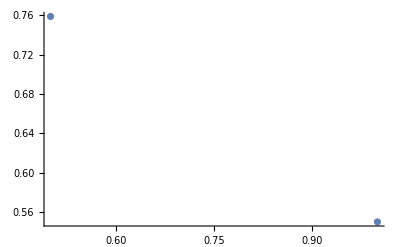

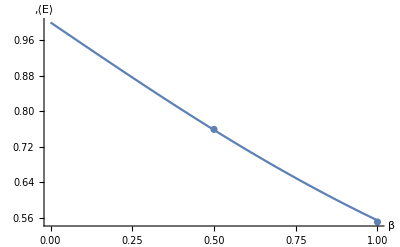

```mathematica
(*twice value of plaquette side*)

L=100;
R0=1;
T0=1;
wilsonlink[β_]:=Module[{F1,F2,h1,h2,act1,act2,plaq,a1,a2,r,g,f,J,ϵ,q},(*Initial lattice config.*)

F1=Table[If[Xor[EvenQ[i],EvenQ[j]],1,0],{i,L},{j,L}];
F2=Table[If[Xor[EvenQ[i],EvenQ[j]],Exp[I*RandomReal[{-Pi,Pi}]],0],{i,L},{j,L}];
(*Wilson Loop 1x1 Action*)h1[k_,i_,j_]:=Module[{p},p[n_,m_]:=Part[k,Mod[i+n,L,1],Mod[j+m,L,1]];
1-Re[p[1,0]**p[2,1]**p[1,2]*p[0,1]]];
(*WilsonLoopRxT*)h2[k_,i_,j_,R_,T_]:=Module[{p},p[n_,m_]:=Part[k,Mod[i+n,L,1],Mod[j+m,L,1]];
Re[Product[p[x,0]**p[x,2T],{x,1,2R,2}]*Product[p[0,x]*(p[2R,x])*,{x,1,2T,2}]]];
plaq[k_]:=Table[h1[k,i,j],{i,1,L,2},{j,1,L,2}];
(*Average Expectated Value*)
act1[k_]:=Sum[If[OddQ[i]&&OddQ[j],h1[k,i,j],0],{i,L},{j,L}]/((L/2)^2);
act2[k_]:=Sum[If[OddQ[i]&&OddQ[j],(1/2)*(h2[k,i,j,R0,T0]+h2[k,i,j,T0,R0]),0],{i,L},{j,L}]/((L/2)^2);
(*Initializaze lattice data*)
a1=List[act1[F1]];
a2=List[act1[F2]];
(*"Monte Carlo" Rejection Sampling*)
r[t_]:=Module[{o},While[True,o=RandomReal[{-Pi,Pi}];
If[RandomReal[]<Exp[β*t*(Cos[o]-1)],Break[]];];
Return[o]];
(*Generating Rule For Links*)
g[k_,i_,j_]:=Module[{p,d1,d2},p[n_,m_]:=Part[k,Mod[i+n,L,1],Mod[j+m,L,1]];
d1:=p[0,-2]**p[1,-1]**p[-1,-1]+p[0,2]**p[1,1]*p[-1,1]*;
d2:=p[2,0]**p[1,1]*p[1,-1]*+p[-2,0]**p[-1,-1]*p[-1,1]*;
Which[
EvenQ[i]&&OddQ[j],Exp[I*r[Abs[d1]]]*(d1*/Abs[d1]),
EvenQ[j]&&OddQ[i],Exp[I*r[Abs[d2]]]*(d2*/Abs[d2]),
True,0]];
(*Sweep Lattice*)
f[m_]:=Module[{s},
s=m;
For[i=1,i<L+1,i++,
For[j=1,j<L+1,j++,
s[[i,j]]=g[s,i,j];
];];
s
];

(*Run Simulation max J Times*)
J=80;
ϵ=0.01;
For[q=0,q<J,q++,
F1=f[F1];
a1=Append[a1,act1[F1]];
F2=f[F2];
a2=Append[a2,act1[F2]];
If[Abs[(a1[[-1]]-a2[[-1]])/(a1[[-1]]+a2[[-1]])]<ϵ&&Abs[(a1[[-1]]-a1[[-2]])/(a1[[-1]]+a1[[-2]])]<ϵ&&Abs[(a2[[-1]]-a2[[-2]])/(a2[[-1]]+a2[[-2]])]<ϵ,Break[]]
];
Print[Length[a1]];
(act1[F1]+act1[F2])/2
];
range=1;
data=Table[{β,wilsonlink[β]},{β,0.5,range,0.5}];
ListPlot[data,PlotRange->All]
f[b_]:=1-(BesselI[b,1]/BesselI[b,0]);
Show[Plot[f[b],{b,0,range}],ListPlot[data,PlotRange->All],PlotRange->All,AxesOrigin->{0,0},AxesStyle-> Thick, TicksStyle->Thick,LabelStyle->Directive[Black,Bold, Medium],AxesLabel->{"β",",⟨E⟩"}]
```